```mathematica
WE={D[u[x,t],{t,2}]-1/25( D[u[x,t],{x,2}])==0}
```

{u^(0,2)[x,t]-1/25 u^(2,0)[x,t]==0}

```mathematica
bc={u[0,t]==0,u[1,t]==0};
```

```mathematica
ic={u[x,0]==10000Sin[1/10x(x-1)]^2,Evaluate[D[u[x,t],t]/.t->0]==1000Sin[1/10  x(x-1)]^2}
```

{u[x,0]==10000 Sin[1/10 (-1+x) x]^2,u^(0,1)[x,0]==1000 Sin[1/10 (-1+x) x]^2}

```mathematica
NDSolve[Flatten[{WE,bc,ic}],u,{x,0,1},{t,0,1}]
```

NDSolve::eerr: Warning: scaled local spatial error estimate of 15.998 at t = 1. in the direction of independent variable x is much greater than the prescribed error tolerance. Grid spacing with 25 points may be too large to achieve the desired accuracy or precision. A singularity may have formed or a smaller grid spacing can be specified using the MaxStepSize or MinPoints method options.

{{u→InterpolatingFunction[{{0., 1.}, {0., 1.}}, <>]}}

```mathematica
usol=First[u/.NDSolve[Flatten[{WE,bc,ic}],u,{x,0,1},{t,0,1}]]
```

NDSolve::eerr: Warning: scaled local spatial error estimate of 15.998 at t = 1. in the direction of independent variable x is much greater than the prescribed error tolerance. Grid spacing with 25 points may be too large to achieve the desired accuracy or precision. A singularity may have formed or a smaller grid spacing can be specified using the MaxStepSize or MinPoints method options.

InterpolatingFunction[{{0., 1.}, {0., 1.}}, <>]

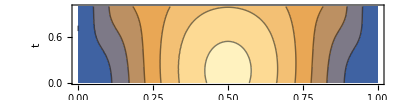

```mathematica
ContourPlot[usol[x,t],{x,0,1},{t,0,1},BaseStyle->FontSize->22,FrameLabel->{"x","t"},PlotLegends->Automatic,LabelStyle->FontSize->18,AspectRatio->1/4]
```

```mathematica
Plot3D[usol[x,t],{x,0,1},{t,0,1},AxesLabel->{x,t}]
```

-Graphics3D-

```mathematica
Length[Table[i,{i,0,1,1/10}]]
```

11

```mathematica
For[gridres=10,gridres<110,gridres+=10,
grid=Table[t,{t,0,1,1/gridres}];
tab=Table[usol[x,t],{x,grid},{t,grid}]
SetDirectory[NotebookDirectory[]];Export[StringJoin["wolfram_sln/","wave_sln_",ToString[gridres],".csv"],tab]
]
```

```mathematica
usol[x,t][0]
```

InterpolatingFunction[{{0., 1.}, {0., 1.}}, <>][x,t][0]

```mathematica
grid=Table[t,{t,0,1,1/10}];
tab=Table[usol[x,t],{x,grid},{t,grid}]
```

{{0.,0.,0.,0.,0.,0.,0.,0.,0.,-1.11022×10^-16,0.},{0.809978,0.836287,0.90013,1.00368,1.14566,1.31729,1.50101,1.67308,1.81071,1.89986,1.94001},{2.55978,2.58701,2.61767,2.65238,2.69211,2.73836,2.79329,2.85957,2.93926,3.03163,3.13032},{4.40935,4.44298,4.45587,4.44836,4.42119,4.37555,4.31297,4.23543,4.14528,4.04537,3.93905},{5.75889,5.79876,5.8034,5.77296,5.70804,5.60968,5.47927,5.31864,5.13002,4.91604,4.67975},{6.2487,6.29105,6.29334,6.25565,6.17856,6.06303,5.91042,5.7225,5.50146,5.24987,4.97074},{5.75889,5.79876,5.8034,5.77296,5.70804,5.60968,5.47927,5.31864,5.13002,4.91604,4.67975},{4.40935,4.44298,4.45587,4.44836,4.42119,4.37555,4.31297,4.23543,4.14528,4.04537,3.93905},{2.55978,2.58701,2.61767,2.65238,2.69211,2.73836,2.79329,2.85957,2.93926,3.03163,3.13032},{0.809978,0.836287,0.90013,1.00368,1.14566,1.31729,1.50101,1.67308,1.81071,1.89986,1.94001},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}}

```mathematica
Table[usol[x,t],{x,grid},{t,1}]
```

{{0.},{1.94001},{3.13032},{3.93905},{4.67975},{4.97074},{4.67975},{3.93905},{3.13032},{1.94001},{0.}}